# Homework 2 Problem 3

In this problem we focus on trying to find the self capacitance of a prolate and oblate spheroid. Phillip I will not lie to you, I do not know how to do this and I kinda want to focus on other things in my life so what I did was I found a compendium of self capacitances in the “Formulas for Computing Capacitance and Inductance” by the United States Department of Commerce (https://nvlpubs.nist.gov/nistpubs/Legacy/circ/nbscircular544.pdf). I used the equations here (1.0-1.20) to make the plots you’ll see here.

## Part a

We start with the capacitance of an oblate spheroid. Equation 1.17 in the cited compendium yields
						
We know that we want to plot as a function of eccentricity which is  so we can factor that out of the above expression and that will give us...
						    
So we can plot this pretty quickly just from -1 to 1 because eccentricity shouldn’t be larger.

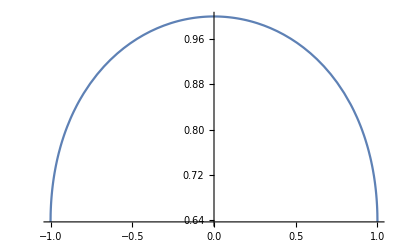

```mathematica
Plot[e/ArcSin[e],{e,-1,1}]
```

We can do the same thing using equation 1.18 for the prolate case...

Which as a function of the eccentricity becomes the following plot

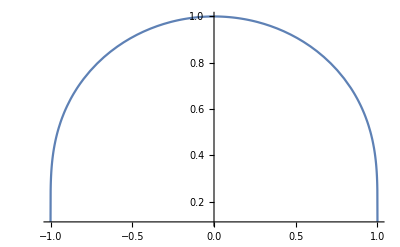

```mathematica
Plot[e/Log[(1+e)/(√(1-e^2))],{e,-1,1}]
```

This is as far as I go in this problem but the plots are interesting. Capacitance as a function of eccentricity where the capacitance is highest in both cases at zero eccentricity. Implications are interesting.